

```mathematica
Plot[x,{x,-2,2}]
```

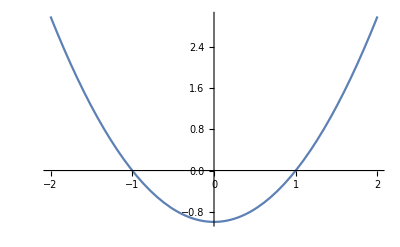

```mathematica
Plot[x^2-1,{x,-2,2}]
```

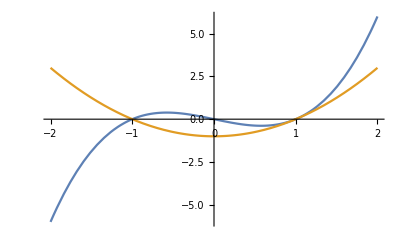

```mathematica
Plot[{x^3-x,x^2-1},{x,-2,2}]
```

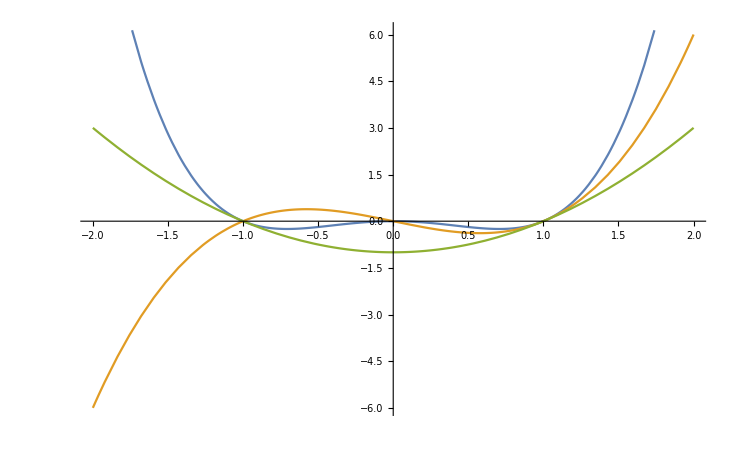

```mathematica
Plot[{x^4-x^2,x^3-x,x^2-1},{x,-2,2}]
```

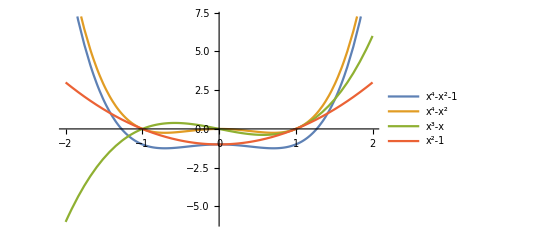

```mathematica
Plot[{x^4-x^2-1,x^4-x^2,x^3-x,x^2-1},{x,-2,2},PlotLegends->"Expressions"]
```

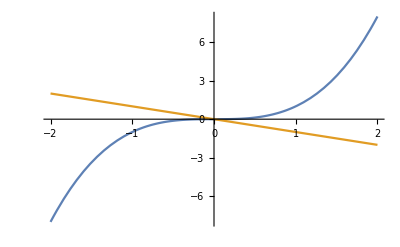

```mathematica
Plot[{x^3,-x},{x,-2,2}]
```

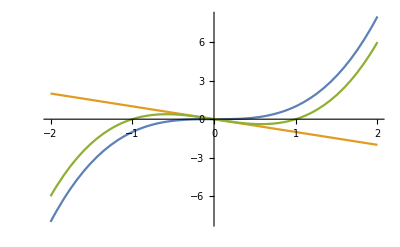

```mathematica
Plot[{x^3,-x,x^3-x},{x,-2,2}]
```

```mathematica
{x^3,-x}/(Total@{x^3,-x})
```

{x^3/(-x+x^3),-x/(-x+x^3)}

```mathematica
{Abs[x^3],Abs[-x]}/(Total@{Abs[x^3],Abs[-x]})
```

{Abs[x]^3/(Abs[x]+Abs[x]^3),Abs[x]/(Abs[x]+Abs[x]^3)}

```mathematica
FullSimplify[{Abs[x]^3/(Abs[x]+Abs[x]^3),Abs[x]/(Abs[x]+Abs[x]^3)},x∈Reals]
```

{x^2/(1+x^2),1/(1+x^2)}

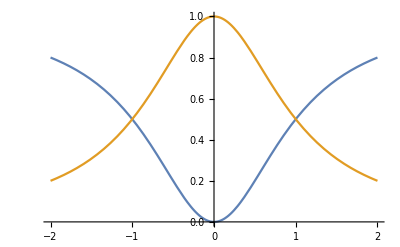

```mathematica
Plot[{x^2/(1+x^2),1/(1+x^2)},{x,-2,2}]
```

```mathematica
FullSimplify[{x^2/(1+x^2),1/(1+x^2)}/.x->a,a∈Reals]
```

{a^2/(1+a^2),1/(1+a^2)}

```mathematica
Total@{a^2/(1+a^2),1/(1+a^2)}==1
```

1/(1+a^2)+a^2/(1+a^2)==1

```mathematica
Reduce[1/(1+a^2)+a^2/(1+a^2)==1,a]
```

True

```mathematica
Collect[1/(1+a^2)+a^2/(1+a^2)]
```

Collect::argbu: Collect called with 1 argument; between 2 and 4 arguments are expected.

Collect[1/(1+a^2)+a^2/(1+a^2)]

```mathematica
1/(1+a^2)+a^2/(1+a^2)
```

1/(1+a^2)+a^2/(1+a^2)

```mathematica
Simplify[1/(1+a^2)+a^2/(1+a^2)]
```

1

```mathematica
Plot[{x^2/(1+x^2),1/(1+x^2)},{x,-2,2}]
```

```mathematica
Series[Sin[x],{x,0,10}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11

```mathematica
Normal[x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880

```mathematica
Abs[{x,-x^3/6,x^5/120,-x^7/5040,x^9/362880}]
```

{Abs[x],Abs[x]^3/6,Abs[x]^5/120,Abs[x]^7/5040,Abs[x]^9/362880}

```mathematica
{Abs[x],Abs[x]^3/6,Abs[x]^5/120,Abs[x]^7/5040,Abs[x]^9/362880}/(Total@{Abs[x],Abs[x]^3/6,Abs[x]^5/120,Abs[x]^7/5040,Abs[x]^9/362880})
```

{Abs[x]/(Abs[x]+Abs[x]^3/6+Abs[x]^5/120+Abs[x]^7/5040+Abs[x]^9/362880),Abs[x]^3/(6 (Abs[x]+Abs[x]^3/6+Abs[x]^5/120+Abs[x]^7/5040+Abs[x]^9/362880)),Abs[x]^5/(120 (Abs[x]+Abs[x]^3/6+Abs[x]^5/120+Abs[x]^7/5040+Abs[x]^9/362880)),Abs[x]^7/(5040 (Abs[x]+Abs[x]^3/6+Abs[x]^5/120+Abs[x]^7/5040+Abs[x]^9/362880)),Abs[x]^9/(362880 (Abs[x]+Abs[x]^3/6+Abs[x]^5/120+Abs[x]^7/5040+Abs[x]^9/362880))}

```mathematica
FullSimplify[
{Abs[x]/(Abs[x]+Abs[x]^3/6+Abs[x]^5/120+Abs[x]^7/5040+Abs[x]^9/362880),Abs[x]^3/(6 (Abs[x]+Abs[x]^3/6+Abs[x]^5/120+Abs[x]^7/5040+Abs[x]^9/362880)),Abs[x]^5/(120 (Abs[x]+Abs[x]^3/6+Abs[x]^5/120+Abs[x]^7/5040+Abs[x]^9/362880)),Abs[x]^7/(5040 (Abs[x]+Abs[x]^3/6+Abs[x]^5/120+Abs[x]^7/5040+Abs[x]^9/362880)),Abs[x]^9/(362880 (Abs[x]+Abs[x]^3/6+Abs[x]^5/120+Abs[x]^7/5040+Abs[x]^9/362880))}
,x∈Reals]
```

{362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)}

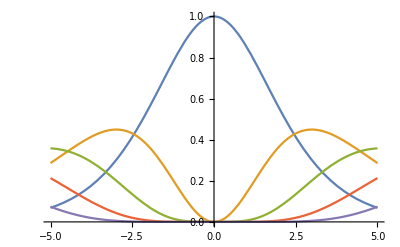

```mathematica
Plot[{362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)}
,{x,-5,5}]
```

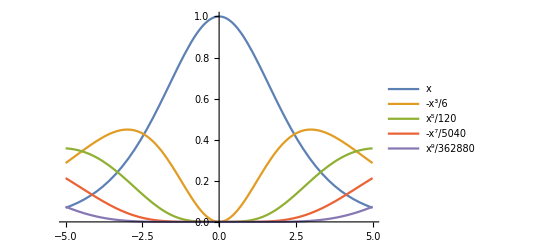

```mathematica
Plot[{362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)}
,{x,-5,5},PlotLegends->{x,-x^3/6,x^5/120,-x^7/5040,x^9/362880}]
```

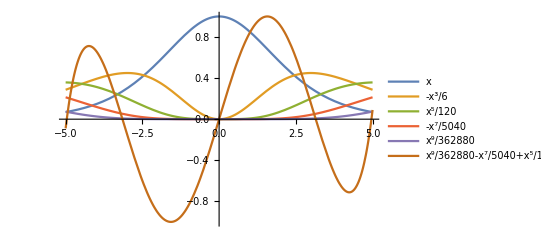

```mathematica
Plot[{362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8),x-x^3/6+x^5/120-x^7/5040+x^9/362880}
,{x,-5,5},PlotLegends->{x,-x^3/6,x^5/120,-x^7/5040,x^9/362880,x-x^3/6+x^5/120-x^7/5040+x^9/362880}]
```

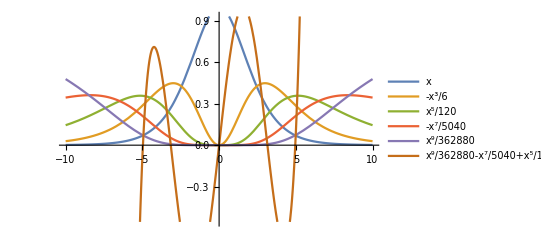

```mathematica
Plot[{362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8),x-x^3/6+x^5/120-x^7/5040+x^9/362880}
,{x,-10,10}
,PlotLegends->{x,-x^3/6,x^5/120,-x^7/5040,x^9/362880,x-x^3/6+x^5/120-x^7/5040+x^9/362880}]
```

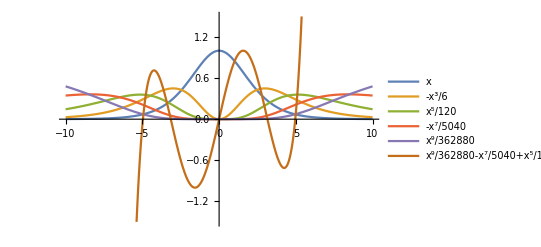

```mathematica
Plot[{362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8),x-x^3/6+x^5/120-x^7/5040+x^9/362880}
,{x,-10,10}
,PlotLegends->{x,-x^3/6,x^5/120,-x^7/5040,x^9/362880,x-x^3/6+x^5/120-x^7/5040+x^9/362880}
,PlotRange->{{-10,10},{-1.5,1.5}}]
```

```mathematica
Total@{362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)}==1/.x->a
```

362880/(362880+60480 a^2+3024 a^4+72 a^6+a^8)+(60480 a^2)/(362880+60480 a^2+3024 a^4+72 a^6+a^8)+(3024 a^4)/(362880+60480 a^2+3024 a^4+72 a^6+a^8)+(72 a^6)/(362880+60480 a^2+3024 a^4+72 a^6+a^8)+a^8/(362880+60480 a^2+3024 a^4+72 a^6+a^8)==1

```mathematica
Reduce[%31]
```

True

```mathematica
y''[x]/((√(1+y'[x]^2))^3)
```

y''[x]/((1+y'[x]^2)^(3/2))

```mathematica
Normalize@{1,y'[t]}.Normalize@{10,y''[t]}
```

10/(√(1+Abs[y'[t]]^2) √(100+Abs[y''[t]]^2))+(y'[t] y''[t])/(√(1+Abs[y'[t]]^2) √(100+Abs[y''[t]]^2))

```mathematica
Normalize@{1,y'[t]}.Normalize@{0,y''[t]}
```

(y'[t] y''[t])/(√(1+Abs[y'[t]]^2) Abs[y''[t]])

```mathematica
FullSimplify[(y'[t] y''[t])/(√(1+Abs[y'[t]]^2) Abs[y''[t]]),{t,y[t],y'[t],y''[t]}∈Reals]
```

(Sign[y''[t]] y'[t])/(√(1+y'[t]^2))

```mathematica
Map[Function[y,y''[x]/((1+y'[x]^2)^(3/2))],{x,-x^3/6,x^5/120,-x^7/5040,x^9/362880}]
```

{x''[x]/((1+x'[x]^2)^(3/2)),((-x^3/6)''[x])/((1+((-x^3/6)'[x])^2)^(3/2)),((x^5/120)''[x])/((1+((x^5/120)'[x])^2)^(3/2)),((-x^7/5040)''[x])/((1+((-x^7/5040)'[x])^2)^(3/2)),((x^9/362880)''[x])/((1+((x^9/362880)'[x])^2)^(3/2))}

```mathematica
Map[Function[y,y''/((1+y'^2)^(3/2))],{x,-x^3/6,x^5/120,-x^7/5040,x^9/362880}]
```

{x''/((1+(x')^2)^(3/2)),((-x^3/6)'')/((1+((-x^3/6)')^2)^(3/2)),((x^5/120)'')/((1+((x^5/120)')^2)^(3/2)),((-x^7/5040)'')/((1+((-x^7/5040)')^2)^(3/2)),((x^9/362880)'')/((1+((x^9/362880)')^2)^(3/2))}

```mathematica
Map[Function[x,#]&,{x,-x^3/6,x^5/120,-x^7/5040,x^9/362880}]
```

{Function[x,x],Function[x,-x^3/6],Function[x,x^5/120],Function[x,-x^7/5040],Function[x,x^9/362880]}

```mathematica
Map[Function[y,y''[x]/((1+y'[x]^2)^(3/2))],{Function[x,x],Function[x,-x^3/6],Function[x,x^5/120],Function[x,-x^7/5040],Function[x,x^9/362880]}]
```

{0,-x/((1+x^4/4)^(3/2)),x^3/(6 (1+x^8/576)^(3/2)),-x^5/(120 (1+x^12/518400)^(3/2)),x^7/(5040 (1+x^16/1625702400)^(3/2))}

```mathematica
Map[Function[y,Abs[y''[x]/((1+y'[x]^2)^(3/2))]],{Function[x,x],Function[x,-x^3/6],Function[x,x^5/120],Function[x,-x^7/5040],Function[x,x^9/362880]}]
```

{0,Abs[x/((1+x^4/4)^(3/2))],1/6 Abs[x^3/((1+x^8/576)^(3/2))],1/120 Abs[x^5/((1+x^12/518400)^(3/2))],Abs[x^7/((1+x^16/1625702400)^(3/2))]/5040}

```mathematica
FullSimplify[{0,Abs[x/((1+x^4/4)^(3/2))],1/6 Abs[x^3/((1+x^8/576)^(3/2))],1/120 Abs[x^5/((1+x^12/518400)^(3/2))],Abs[x^7/((1+x^16/1625702400)^(3/2))]/5040},x∈Reals]
```

{0,(8 Abs[x])/((4+x^4)^(3/2)),(2304 Abs[x]^3)/((576+x^8)^(3/2)),(3110400 Abs[x]^5)/((518400+x^12)^(3/2)),Abs[x]^7/(5040 (1+x^16/1625702400)^(3/2))}

```mathematica
{0,(8 Abs[x])/((4+x^4)^(3/2)),(2304 Abs[x]^3)/((576+x^8)^(3/2)),(3110400 Abs[x]^5)/((518400+x^12)^(3/2)),Abs[x]^7/(5040 (1+x^16/1625702400)^(3/2))}/(Total@{0,(8 Abs[x])/((4+x^4)^(3/2)),(2304 Abs[x]^3)/((576+x^8)^(3/2)),(3110400 Abs[x]^5)/((518400+x^12)^(3/2)),Abs[x]^7/(5040 (1+x^16/1625702400)^(3/2))})
```

{0,(8 Abs[x])/((4+x^4)^(3/2) ((8 Abs[x])/((4+x^4)^(3/2))+(2304 Abs[x]^3)/((576+x^8)^(3/2))+(3110400 Abs[x]^5)/((518400+x^12)^(3/2))+Abs[x]^7/(5040 (1+x^16/1625702400)^(3/2)))),(2304 Abs[x]^3)/((576+x^8)^(3/2) ((8 Abs[x])/((4+x^4)^(3/2))+(2304 Abs[x]^3)/((576+x^8)^(3/2))+(3110400 Abs[x]^5)/((518400+x^12)^(3/2))+Abs[x]^7/(5040 (1+x^16/1625702400)^(3/2)))),(3110400 Abs[x]^5)/((518400+x^12)^(3/2) ((8 Abs[x])/((4+x^4)^(3/2))+(2304 Abs[x]^3)/((576+x^8)^(3/2))+(3110400 Abs[x]^5)/((518400+x^12)^(3/2))+Abs[x]^7/(5040 (1+x^16/1625702400)^(3/2)))),Abs[x]^7/(5040 (1+x^16/1625702400)^(3/2) ((8 Abs[x])/((4+x^4)^(3/2))+(2304 Abs[x]^3)/((576+x^8)^(3/2))+(3110400 Abs[x]^5)/((518400+x^12)^(3/2))+Abs[x]^7/(5040 (1+x^16/1625702400)^(3/2))))}

```mathematica
FullSimplify[{0,(8 Abs[x])/((4+x^4)^(3/2) ((8 Abs[x])/((4+x^4)^(3/2))+(2304 Abs[x]^3)/((576+x^8)^(3/2))+(3110400 Abs[x]^5)/((518400+x^12)^(3/2))+Abs[x]^7/(5040 (1+x^16/1625702400)^(3/2)))),(2304 Abs[x]^3)/((576+x^8)^(3/2) ((8 Abs[x])/((4+x^4)^(3/2))+(2304 Abs[x]^3)/((576+x^8)^(3/2))+(3110400 Abs[x]^5)/((518400+x^12)^(3/2))+Abs[x]^7/(5040 (1+x^16/1625702400)^(3/2)))),(3110400 Abs[x]^5)/((518400+x^12)^(3/2) ((8 Abs[x])/((4+x^4)^(3/2))+(2304 Abs[x]^3)/((576+x^8)^(3/2))+(3110400 Abs[x]^5)/((518400+x^12)^(3/2))+Abs[x]^7/(5040 (1+x^16/1625702400)^(3/2)))),Abs[x]^7/(5040 (1+x^16/1625702400)^(3/2) ((8 Abs[x])/((4+x^4)^(3/2))+(2304 Abs[x]^3)/((576+x^8)^(3/2))+(3110400 Abs[x]^5)/((518400+x^12)^(3/2))+Abs[x]^7/(5040 (1+x^16/1625702400)^(3/2))))},x∈Reals]
```

{0,1/((4+x^4)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(288 x^2)/((576+x^8)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(388800 x^4)/((518400+x^12)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(1625702400 x^6)/((1625702400+x^16)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2)))))}

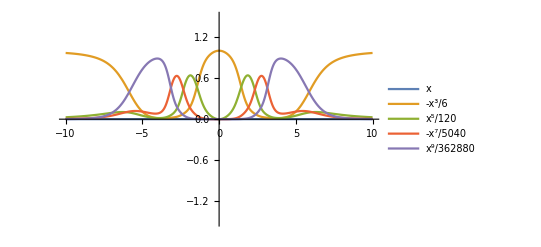

```mathematica
Plot[{0,1/((4+x^4)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(288 x^2)/((576+x^8)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(388800 x^4)/((518400+x^12)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(1625702400 x^6)/((1625702400+x^16)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2)))))}
,{x,-10,10}
,PlotLegends->{x,-x^3/6,x^5/120,-x^7/5040,x^9/362880,x-x^3/6+x^5/120-x^7/5040+x^9/362880}
,PlotRange->{{-10,10},{-1.5,1.5}}]
```

```mathematica
x-x^3/6+x^5/120-x^7/5040+x^9/362880
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880

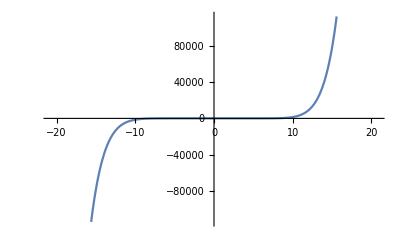

```mathematica
Plot[x-x^3/6+x^5/120-x^7/5040+x^9/362880,{x,-20.784609690826528,20.784609690826528}]
```

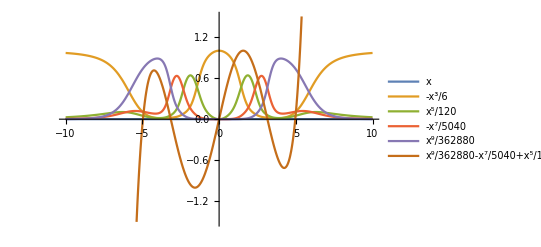

```mathematica
Plot[{0,1/((4+x^4)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(288 x^2)/((576+x^8)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(388800 x^4)/((518400+x^12)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(1625702400 x^6)/((1625702400+x^16)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),x-x^3/6+x^5/120-x^7/5040+x^9/362880}
,{x,-10,10}
,PlotLegends->{x,-x^3/6,x^5/120,-x^7/5040,x^9/362880,x-x^3/6+x^5/120-x^7/5040+x^9/362880}
,PlotRange->{{-10,10},{-1.5,1.5}}]
```

```mathematica
D[x-x^3/6+x^5/120-x^7/5040+x^9/362880,x]
```

1-x^2/2+x^4/24-x^6/720+x^8/40320

```mathematica
D[1-x^2/2+x^4/24-x^6/720+x^8/40320,x]
```

-x+x^3/6-x^5/120+x^7/5040

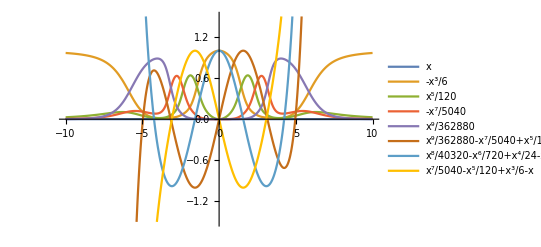

```mathematica
Plot[{0,1/((4+x^4)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(288 x^2)/((576+x^8)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(388800 x^4)/((518400+x^12)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(1625702400 x^6)/((1625702400+x^16)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),x-x^3/6+x^5/120-x^7/5040+x^9/362880,1-x^2/2+x^4/24-x^6/720+x^8/40320,-x+x^3/6-x^5/120+x^7/5040}
,{x,-10,10}
,PlotLegends->{x,-x^3/6,x^5/120,-x^7/5040,x^9/362880,x-x^3/6+x^5/120-x^7/5040+x^9/362880,1-x^2/2+x^4/24-x^6/720+x^8/40320,-x+x^3/6-x^5/120+x^7/5040}
,PlotRange->{{-10,10},{-1.5,1.5}}]
```

```mathematica
Total@{0,1/((4+x^4)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(288 x^2)/((576+x^8)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(388800 x^4)/((518400+x^12)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(1625702400 x^6)/((1625702400+x^16)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2)))))}==1
```

1/((4+x^4)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2)))))+(288 x^2)/((576+x^8)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2)))))+(388800 x^4)/((518400+x^12)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2)))))+(1625702400 x^6)/((1625702400+x^16)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2)))))==1

```mathematica
Reduce[%53]
```

True

```mathematica
Map[Function[y,y''[x]/((1+y'[x]^2)^(3/2))],{Function[x,x],Function[x,-x^3/6],Function[x,x^5/120],Function[x,-x^7/5040],Function[x,x^9/362880]}]
```

{0,-x/((1+x^4/4)^(3/2)),x^3/(6 (1+x^8/576)^(3/2)),-x^5/(120 (1+x^12/518400)^(3/2)),x^7/(5040 (1+x^16/1625702400)^(3/2))}

```mathematica
{0,-x/((1+x^4/4)^(3/2)),x^3/(6 (1+x^8/576)^(3/2)),-x^5/(120 (1+x^12/518400)^(3/2)),x^7/(5040 (1+x^16/1625702400)^(3/2))}/(Total@{0,-x/((1+x^4/4)^(3/2)),x^3/(6 (1+x^8/576)^(3/2)),-x^5/(120 (1+x^12/518400)^(3/2)),x^7/(5040 (1+x^16/1625702400)^(3/2))})
```

{0,-x/((1+x^4/4)^(3/2) (-x/((1+x^4/4)^(3/2))+x^3/(6 (1+x^8/576)^(3/2))-x^5/(120 (1+x^12/518400)^(3/2))+x^7/(5040 (1+x^16/1625702400)^(3/2)))),x^3/(6 (1+x^8/576)^(3/2) (-x/((1+x^4/4)^(3/2))+x^3/(6 (1+x^8/576)^(3/2))-x^5/(120 (1+x^12/518400)^(3/2))+x^7/(5040 (1+x^16/1625702400)^(3/2)))),-x^5/(120 (1+x^12/518400)^(3/2) (-x/((1+x^4/4)^(3/2))+x^3/(6 (1+x^8/576)^(3/2))-x^5/(120 (1+x^12/518400)^(3/2))+x^7/(5040 (1+x^16/1625702400)^(3/2)))),x^7/(5040 (1+x^16/1625702400)^(3/2) (-x/((1+x^4/4)^(3/2))+x^3/(6 (1+x^8/576)^(3/2))-x^5/(120 (1+x^12/518400)^(3/2))+x^7/(5040 (1+x^16/1625702400)^(3/2))))}

```mathematica
FullSimplify[{0,-x/((1+x^4/4)^(3/2) (-x/((1+x^4/4)^(3/2))+x^3/(6 (1+x^8/576)^(3/2))-x^5/(120 (1+x^12/518400)^(3/2))+x^7/(5040 (1+x^16/1625702400)^(3/2)))),x^3/(6 (1+x^8/576)^(3/2) (-x/((1+x^4/4)^(3/2))+x^3/(6 (1+x^8/576)^(3/2))-x^5/(120 (1+x^12/518400)^(3/2))+x^7/(5040 (1+x^16/1625702400)^(3/2)))),-x^5/(120 (1+x^12/518400)^(3/2) (-x/((1+x^4/4)^(3/2))+x^3/(6 (1+x^8/576)^(3/2))-x^5/(120 (1+x^12/518400)^(3/2))+x^7/(5040 (1+x^16/1625702400)^(3/2)))),x^7/(5040 (1+x^16/1625702400)^(3/2) (-x/((1+x^4/4)^(3/2))+x^3/(6 (1+x^8/576)^(3/2))-x^5/(120 (1+x^12/518400)^(3/2))+x^7/(5040 (1+x^16/1625702400)^(3/2))))},x∈Reals]
```

{0,-1/((4+x^4)^(3/2) (-1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))-(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(288 x^2)/((576+x^8)^(3/2) (-1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))-(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),-(388800 x^4)/((518400+x^12)^(3/2) (-1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))-(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(1625702400 x^6)/((1625702400+x^16)^(3/2) (-1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))-(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2)))))}

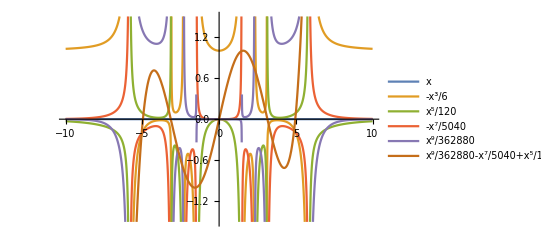

```mathematica
Plot[{0,-1/((4+x^4)^(3/2) (-1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))-(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(288 x^2)/((576+x^8)^(3/2) (-1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))-(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),-(388800 x^4)/((518400+x^12)^(3/2) (-1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))-(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(1625702400 x^6)/((1625702400+x^16)^(3/2) (-1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))-(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),x-x^3/6+x^5/120-x^7/5040+x^9/362880}
,{x,-10,10}
,PlotLegends->{x,-x^3/6,x^5/120,-x^7/5040,x^9/362880,x-x^3/6+x^5/120-x^7/5040+x^9/362880}
,PlotRange->{{-10,10},{-1.5,1.5}}]
```